{{Lepirudin,Dabigatran etexilate,2},{Lepirudin,Drotrecogin alfa,2},{Lepirudin,Zinc acetate,2},{Lepirudin,Human C1-esterase inhibitor,2},{Lepirudin,Copper,2},{Lepirudin,Enoxaparin,2},{Lepirudin,Coagulation Factor IX Human,2},16829,{Mobocertinib,Osimertinib,1},{Mobocertinib,Amivantamab,1},{Lisocabtagene maraleucel,Tremelimumab,1},{Lisocabtagene maraleucel,Tafasitamab,2},{Lisocabtagene maraleucel,Blinatumomab,2},{Lisocabtagene maraleucel,Ipilimumab,1},{Amivantamab,Osimertinib,1}}
 |  |  |  |

{Lepirudin→Dabigatran etexilate,Lepirudin→Drotrecogin alfa,Lepirudin→Zinc acetate,Lepirudin→Human C1-esterase inhibitor,Lepirudin→Copper,Lepirudin→Enoxaparin,Lepirudin→Coagulation Factor IX Human,Lepirudin→Menadione,Lepirudin→Thrombomodulin Alfa,16826,Loncastuximab tesirine→Ipilimumab,Mobocertinib→Osimertinib,Mobocertinib→Amivantamab,Lisocabtagene maraleucel→Tremelimumab,Lisocabtagene maraleucel→Tafasitamab,Lisocabtagene maraleucel→Blinatumomab,Lisocabtagene maraleucel→Ipilimumab,Amivantamab→Osimertinib}
 |  |  |  |

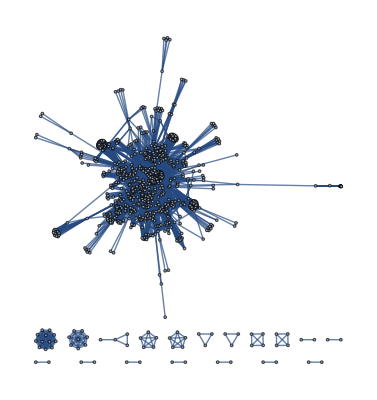

```mathematica
dataDrDiGe519=Import["C:\\DrDiGe\\dr-di-ge-519.csv"]
edgesDrDiGe519= Map[#[[1]]->#[[2]]&,dataDrDiGe519]
gDrDiGe519=UndirectedGraph[edgesDrDiGe519]
```

```mathematica
CommunityGraphPlot[gDrDiGe519,Method->{"Modularity","Weighted"->True}, ImageSize->1200, VertexSize->Larger,PlotLabel->Style["DrugBank 5.1.9 DDSN network based on gene-disease",FontSize->18],CommunityRegionStyle-> LightGray,CommunityLabels->{"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19", "20",  "21", "22", "23", "24", "25", "26", "27", "28", "29", "30", "31", "32", "33", "34", "35", "36", "37", "38", "39", "40", "41", "42", "43", "44", "45", "46", "47", "48", "49", "50", "51", "52", "53", "54", "55", "56", "57", "58", "59", "60", "61", "62", "63", "64", "65", "66", "67", "68", "69", "70", "71", "72", "73", "74", "75", "76", "77", "78", "79", "80"}]
```

-Graphics-

```mathematica
CommunityGraphPlot[gDrDiGe519,VertexStyle->{EdgeForm[Black]},Method->{"Modularity","Weighted"->True}, PlotTheme-> "Default"]
```

-Graphics-

```mathematica
CommunityGraphPlot[gDrDiGe519,Method->{"Modularity","Weighted"->True}, PlotTheme-> "Default", CommunityRegionStyle-> LightGray,CommunityBoundaryStyle->None, VertexStyle->EdgeForm[Dashed]]
```

-Graphics-

```mathematica
cg=FindGraphCommunities[gDrDiGe519]
```

{{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Cetuximab,Neratinib,Gemtuzumab ozogamicin,Dacomitinib,Sutimlimab,Necitumumab,Brigatinib,Catumaxomab,Mobocertinib,Panitumumab,Alefacept,Bevacizumab,Osimertinib,Amivantamab,Erlotinib,Benralizumab,Zinc chloride,Foreskin keratinocyte (neonatal),Sarilumab,Palivizumab,Zinc sulfate, unspecified form,Fostamatinib,Human immunoglobulin G,Vandetanib,Gefitinib,Zanubrutinib,Alemtuzumab,Afatinib,Etanercept,Lidocaine,Lapatinib,Denileukin diftitox,Duvelisib,Tremelimumab,Pentostatin,Acetylcysteine,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Pazopanib,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Mesalazine,Arsenic trioxide,Nintedanib,Teplizumab,Aldesleukin,Dasatinib,Blinatumomab,Acetylsalicylic acid,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Ponatinib,Basiliximab,Ruxolitinib,Idelalisib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Gestrinone,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Heparin,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aprotinin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Sargramostim,Foreskin fibroblast (neonatal),Clove oil,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Eculizumab,Pegcetacoplan,Ravulizumab,Flavin mononucleotide,Pyridoxal phosphate,Ascorbic acid,Vitamin E,Anisindione,Phylloquinone,Sitaxentan,Teriflunomide,Glasdegib,Artenimol,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Tamoxifen,Sonidegib,Fluocinonide,Ambrisentan,Bosentan,Vismodegib,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Aluminium,Ritodrine,Dimercaprol,Migalastat,Aluminum acetate,Von Willebrand factor human,Flutemetamol (18F),Aluminium phosphate,Florbetaben (18F),Vonicog alfa,Tromethamine,Florbetapir (18F),Sodium tetradecyl sulfate,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Ademetionine,Cysteine,Ecallantide,Lanadelumab,Berotralstat,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,Methyldopa,Carbidopa,Celecoxib,Oseltamivir,Axitinib,Benserazide,Flavin adenine dinucleotide,Ubidecarenone,Carboxin,Dopamine,Disulfiram,Ribostamycin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,Glutathione,Minocycline,Dichloroacetic acid,Glycerin,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Bumetanide,Glyburide,Elexacaftor,Manganese,alpha-Tocopherol succinate,Cholecystokinin,D-alpha-Tocopherol acetate,Cupric Chloride,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Citric acid,Amiloride,Triamterene,Dantrolene,Tetracaine,Dibotermin alfa,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Ampicillin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Asciminib,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Catridecacog,Benzoic acid,Isoprenaline,Neomycin,Cinacalcet,Etelcalcetide,Mercaptopurine,Ibrutinib,Acalabrutinib,Tirbanibulin,Polatuzumab vedotin,Tepotinib,Capmatinib,Crizotinib,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Glycolic acid,Tegafur-uracil,Gimeracil,Ingenol mebutate,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Lorlatinib,Gilteritinib,Ceritinib,Alectinib,Deucravacitinib},{Felodipine,Nitrendipine,Isoflurane,Amlodipine,Quinidine barbiturate,Ethanol,Verapamil,Isradipine,Loperamide,Polyethylene glycol 400,Bepridil,Terazosin,Cyanocobalamin,Methionine,Biotin,Levocarnitine,Valine,Perhexiline,Mecobalamin,Thimerosal,Hydroxocobalamin,Nicotine,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Fluoxetine,Varenicline,Bioallethrin,Thiamylal,Clevidipine,Cinnarizine,Ketoconazole,Dequalinium,Nimodipine,Zonisamide,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Tramadol,Ouabain,Amylmetacresol,Metergoline,Propofol,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Diazoxide,Gliquidone,Lauric acid,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Trimethadione,Methsuximide,Flunarizine,Manidipine,Ethosuximide,Desipramine,Fospropofol,gamma-Hydroxybutyric acid,Allopurinol,Febuxostat,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Procaine,Azacitidine,Flucytosine,Decitabine,Phenformin,Nicorandil,Sodium oxybate},{Insulin human,Thyrotropin alfa,2-mercaptobenzothiazole,Thyroid, porcine,Liotrix,Resorcinol,Methimazole,Triclosan,Dextrothyroxine,Levothyroxine,Carbimazole,Propylthiouracil,Liothyronine,Meprobamate,Levetiracetam,Insulin detemir,Azathioprine,Halothane,Ziconotide,Chromic chloride,Vigabatrin,Thiopental,Topiramate,Sevoflurane,Aspartic acid,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Insulin degludec,Talbutal,Somatrem,Primidone,Glutamic acid,Eszopiclone,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Insulin glulisine,Insulin lispro,Lindane,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Ornithine,Mitapivat,Asparagine,gamma-Aminobutyric acid,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Methohexital,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Meperidine,Amoxapine,Butabarbital,Fluciclovine (18F),Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Clotrimazole,Quinine,Cisatracurium,Fomepizole,Benzoyl peroxide},{NADH,Succinic acid,Chlormerodrin,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Tetracosactide,Hexylresorcinol,Hydroquinone,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Bremelanotide,Azelaic acid,Corticotropin,Xanthinol,Nicotinamide,Benzthiazide,Diclofenamide,Omega-3-carboxylic acids,Vardenafil,Tadalafil,Mycophenolate mofetil,Monobenzone,Bendroflumethiazide,Arbutin,Brinzolamide,Methazolamide,Sodium carbonate,Stiripentol,Tretinoin,Metformin,Voretigene neparvovec,Palmitic Acid,Dexamethasone,Dexamethasone acetate,Seractide acetate,Hyaluronic acid,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide,Finasteride,Dutasteride,Doxapram,Oleic Acid,Tyloxapol,Glycyrrhizic acid},{Spironolactone,Abiraterone,Hydrocortisone valerate,Fluoxymesterone,Hydrocortisone acetate,Hydrocortisone phosphate,Levoketoconazole,Hydrocortisone cypionate,Hydrocortisone probutate,Progesterone,Hydrocortisone butyrate,Flunisolide,Triamcinolone,Loteprednol etabonate,Fluticasone furoate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Mometasone furoate,Betamethasone,Megestrol acetate,Flumethasone,Clobetasol propionate,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Betamethasone phosphate,Segesterone acetate,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Clobetasone,Prednisolone phosphate,Methylprednisolone,Medrysone,Cortisone acetate,Drospirenone,Prednisolone acetate,Fluticasone propionate,Difluocortolone,Diflorasone,Fludrocortisone,Beclomethasone dipropionate,Budesonide,Alclometasone,Deflazacort,Fluticasone,Tixocortol,Rimexolone,Aminoglutethimide,Testosterone enanthate,Eplerenone,Testosterone cypionate,Testosterone,Finerenone,Desoxycorticosterone acetate,Mitotane,Osilodrostat,Metyrapone},{Dexibuprofen,Ibuprofen,Icosapent,Ketorolac,Glycol salicylate,Oxaprozin,Troglitazone,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenylbutazone,Phenyl salicylate,Rosiglitazone,Suprofen,Ketoprofen,Lornoxicam,Tiaprofenic acid,Nabumetone,Trolamine salicylate,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Metamizole,Antipyrine,Flurbiprofen,Balsalazide,Bendazac,Acemetacin,Diclofenac,Salsalate,Diethylcarbamazine,Meloxicam,Choline magnesium trisalicylate,Piroxicam,Indomethacin,Tolfenamic acid,Carprofen,Mefenamic acid,Minoxidil,Flufenamic acid,Meclofenamic acid,Bromfenac,Antrafenine,Tolmetin,Salicylic acid,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Fenoprofen,Triflusal,Sulfasalazine,Tenoxicam,Pseudoephedrine,Papaverine},{Dronedarone,Carvedilol,Phenylalanine,Tyrosine,Metyrosine,Droxidopa,Norepinephrine,Sapropterin,Haloperidol,Etomidate,Prazosin,Ziprasidone,Apraclonidine,Bromocriptine,Phenoxybenzamine,Oxymetazoline,Clozapine,Rotigotine,Yohimbine,Fenoldopam,Metamfetamine,Risperidone,Quetiapine,Mianserin,Brimonidine,Methotrimeprazine,Epinephrine,Asenapine,Paliperidone,Loxapine,Racepinephrine,Guanfacine,Xylometazoline,Aripiprazole lauroxil,Cabergoline,Apomorphine,Trimipramine,Clonidine,Aripiprazole,Celiprolol,Tolazoline,Guanabenz,Pizotifen,Lisuride},{Captopril,Ramipril,Cilazapril,Lisinopril,Benazepril,Spirapril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Zofenopril,Enalaprilat,Trandolapril,Perindopril,Enalapril},{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin},{Pegfilgrastim,Ibalizumab,Lipegfilgrastim,Filgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim,Alpha-1-proteinase inhibitor,Baclofen},{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline},{Milrinone,Aminophylline,Enoximone,Theophylline,Cilostazol,Oxtriphylline,Anagrelide,Amrinone},{Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine},{Norelgestromin,Phenol,Cefotaxime,Guaiacol,Silver,Patent Blue},{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin},{Phenprocoumon,Phenindione,Warfarin,Dicoumarol,Acenocoumarol},{Pamidronic acid,Risedronic acid,Zoledronic acid,Alendronic acid,Ibandronate},{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin},{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole},{Acarbose,Miglitol,alpha-Arbutin,Scopolamine},{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag},{Vincristine,Cabazitaxel,Podofilox},{Erythrityl tetranitrate,Nesiritide,Vosoritide},{Sermorelin,Tesamorelin},{Botulinum toxin type A,Letibotulinumtoxina},{Choline,Choline salicylate},{Creatine,Guanidine},{Griseofulvin,Anthralin},{Lenalidomide,Denosumab},{Albendazole,Mebendazole},{Methotrexate,Pemetrexed},{Ivosidenib,Olutasidenib}}

```mathematica
For[i=1,i<Length[cg]+1,i++,Print[cg[[i]]]]
```

{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Cetuximab,Neratinib,Gemtuzumab ozogamicin,Dacomitinib,Sutimlimab,Necitumumab,Brigatinib,Catumaxomab,Mobocertinib,Panitumumab,Alefacept,Bevacizumab,Osimertinib,Amivantamab,Erlotinib,Benralizumab,Zinc chloride,Foreskin keratinocyte (neonatal),Sarilumab,Palivizumab,Zinc sulfate, unspecified form,Fostamatinib,Human immunoglobulin G,Vandetanib,Gefitinib,Zanubrutinib,Alemtuzumab,Afatinib,Etanercept,Lidocaine,Lapatinib,Denileukin diftitox,Duvelisib,Tremelimumab,Pentostatin,Acetylcysteine,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Pazopanib,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Mesalazine,Arsenic trioxide,Nintedanib,Teplizumab,Aldesleukin,Dasatinib,Blinatumomab,Acetylsalicylic acid,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Ponatinib,Basiliximab,Ruxolitinib,Idelalisib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Gestrinone,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Heparin,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aprotinin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Sargramostim,Foreskin fibroblast (neonatal),Clove oil,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Eculizumab,Pegcetacoplan,Ravulizumab,Flavin mononucleotide,Pyridoxal phosphate,Ascorbic acid,Vitamin E,Anisindione,Phylloquinone,Sitaxentan,Teriflunomide,Glasdegib,Artenimol,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Tamoxifen,Sonidegib,Fluocinonide,Ambrisentan,Bosentan,Vismodegib,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Aluminium,Ritodrine,Dimercaprol,Migalastat,Aluminum acetate,Von Willebrand factor human,Flutemetamol (18F),Aluminium phosphate,Florbetaben (18F),Vonicog alfa,Tromethamine,Florbetapir (18F),Sodium tetradecyl sulfate,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Ademetionine,Cysteine,Ecallantide,Lanadelumab,Berotralstat,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,Methyldopa,Carbidopa,Celecoxib,Oseltamivir,Axitinib,Benserazide,Flavin adenine dinucleotide,Ubidecarenone,Carboxin,Dopamine,Disulfiram,Ribostamycin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,Glutathione,Minocycline,Dichloroacetic acid,Glycerin,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Bumetanide,Glyburide,Elexacaftor,Manganese,alpha-Tocopherol succinate,Cholecystokinin,D-alpha-Tocopherol acetate,Cupric Chloride,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Citric acid,Amiloride,Triamterene,Dantrolene,Tetracaine,Dibotermin alfa,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Ampicillin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Asciminib,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Catridecacog,Benzoic acid,Isoprenaline,Neomycin,Cinacalcet,Etelcalcetide,Mercaptopurine,Ibrutinib,Acalabrutinib,Tirbanibulin,Polatuzumab vedotin,Tepotinib,Capmatinib,Crizotinib,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Glycolic acid,Tegafur-uracil,Gimeracil,Ingenol mebutate,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Lorlatinib,Gilteritinib,Ceritinib,Alectinib,Deucravacitinib}

{Felodipine,Nitrendipine,Isoflurane,Amlodipine,Quinidine barbiturate,Ethanol,Verapamil,Isradipine,Loperamide,Polyethylene glycol 400,Bepridil,Terazosin,Cyanocobalamin,Methionine,Biotin,Levocarnitine,Valine,Perhexiline,Mecobalamin,Thimerosal,Hydroxocobalamin,Nicotine,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Fluoxetine,Varenicline,Bioallethrin,Thiamylal,Clevidipine,Cinnarizine,Ketoconazole,Dequalinium,Nimodipine,Zonisamide,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Tramadol,Ouabain,Amylmetacresol,Metergoline,Propofol,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Diazoxide,Gliquidone,Lauric acid,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Trimethadione,Methsuximide,Flunarizine,Manidipine,Ethosuximide,Desipramine,Fospropofol,gamma-Hydroxybutyric acid,Allopurinol,Febuxostat,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Procaine,Azacitidine,Flucytosine,Decitabine,Phenformin,Nicorandil,Sodium oxybate}

{Insulin human,Thyrotropin alfa,2-mercaptobenzothiazole,Thyroid, porcine,Liotrix,Resorcinol,Methimazole,Triclosan,Dextrothyroxine,Levothyroxine,Carbimazole,Propylthiouracil,Liothyronine,Meprobamate,Levetiracetam,Insulin detemir,Azathioprine,Halothane,Ziconotide,Chromic chloride,Vigabatrin,Thiopental,Topiramate,Sevoflurane,Aspartic acid,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Insulin degludec,Talbutal,Somatrem,Primidone,Glutamic acid,Eszopiclone,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Insulin glulisine,Insulin lispro,Lindane,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Ornithine,Mitapivat,Asparagine,gamma-Aminobutyric acid,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Methohexital,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Meperidine,Amoxapine,Butabarbital,Fluciclovine (18F),Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Clotrimazole,Quinine,Cisatracurium,Fomepizole,Benzoyl peroxide}

{NADH,Succinic acid,Chlormerodrin,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Tetracosactide,Hexylresorcinol,Hydroquinone,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Bremelanotide,Azelaic acid,Corticotropin,Xanthinol,Nicotinamide,Benzthiazide,Diclofenamide,Omega-3-carboxylic acids,Vardenafil,Tadalafil,Mycophenolate mofetil,Monobenzone,Bendroflumethiazide,Arbutin,Brinzolamide,Methazolamide,Sodium carbonate,Stiripentol,Tretinoin,Metformin,Voretigene neparvovec,Palmitic Acid,Dexamethasone,Dexamethasone acetate,Seractide acetate,Hyaluronic acid,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide,Finasteride,Dutasteride,Doxapram,Oleic Acid,Tyloxapol,Glycyrrhizic acid}

{Spironolactone,Abiraterone,Hydrocortisone valerate,Fluoxymesterone,Hydrocortisone acetate,Hydrocortisone phosphate,Levoketoconazole,Hydrocortisone cypionate,Hydrocortisone probutate,Progesterone,Hydrocortisone butyrate,Flunisolide,Triamcinolone,Loteprednol etabonate,Fluticasone furoate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Mometasone furoate,Betamethasone,Megestrol acetate,Flumethasone,Clobetasol propionate,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Betamethasone phosphate,Segesterone acetate,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Clobetasone,Prednisolone phosphate,Methylprednisolone,Medrysone,Cortisone acetate,Drospirenone,Prednisolone acetate,Fluticasone propionate,Difluocortolone,Diflorasone,Fludrocortisone,Beclomethasone dipropionate,Budesonide,Alclometasone,Deflazacort,Fluticasone,Tixocortol,Rimexolone,Aminoglutethimide,Testosterone enanthate,Eplerenone,Testosterone cypionate,Testosterone,Finerenone,Desoxycorticosterone acetate,Mitotane,Osilodrostat,Metyrapone}

{Dexibuprofen,Ibuprofen,Icosapent,Ketorolac,Glycol salicylate,Oxaprozin,Troglitazone,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenylbutazone,Phenyl salicylate,Rosiglitazone,Suprofen,Ketoprofen,Lornoxicam,Tiaprofenic acid,Nabumetone,Trolamine salicylate,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Metamizole,Antipyrine,Flurbiprofen,Balsalazide,Bendazac,Acemetacin,Diclofenac,Salsalate,Diethylcarbamazine,Meloxicam,Choline magnesium trisalicylate,Piroxicam,Indomethacin,Tolfenamic acid,Carprofen,Mefenamic acid,Minoxidil,Flufenamic acid,Meclofenamic acid,Bromfenac,Antrafenine,Tolmetin,Salicylic acid,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Fenoprofen,Triflusal,Sulfasalazine,Tenoxicam,Pseudoephedrine,Papaverine}

{Dronedarone,Carvedilol,Phenylalanine,Tyrosine,Metyrosine,Droxidopa,Norepinephrine,Sapropterin,Haloperidol,Etomidate,Prazosin,Ziprasidone,Apraclonidine,Bromocriptine,Phenoxybenzamine,Oxymetazoline,Clozapine,Rotigotine,Yohimbine,Fenoldopam,Metamfetamine,Risperidone,Quetiapine,Mianserin,Brimonidine,Methotrimeprazine,Epinephrine,Asenapine,Paliperidone,Loxapine,Racepinephrine,Guanfacine,Xylometazoline,Aripiprazole lauroxil,Cabergoline,Apomorphine,Trimipramine,Clonidine,Aripiprazole,Celiprolol,Tolazoline,Guanabenz,Pizotifen,Lisuride}

{Captopril,Ramipril,Cilazapril,Lisinopril,Benazepril,Spirapril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Zofenopril,Enalaprilat,Trandolapril,Perindopril,Enalapril}

{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin}

{Pegfilgrastim,Ibalizumab,Lipegfilgrastim,Filgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim,Alpha-1-proteinase inhibitor,Baclofen}

{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline}

{Milrinone,Aminophylline,Enoximone,Theophylline,Cilostazol,Oxtriphylline,Anagrelide,Amrinone}

{Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine}

{Norelgestromin,Phenol,Cefotaxime,Guaiacol,Silver,Patent Blue}

{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin}

{Phenprocoumon,Phenindione,Warfarin,Dicoumarol,Acenocoumarol}

{Pamidronic acid,Risedronic acid,Zoledronic acid,Alendronic acid,Ibandronate}

{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin}

{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole}

{Acarbose,Miglitol,alpha-Arbutin,Scopolamine}

{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag}

{Vincristine,Cabazitaxel,Podofilox}

{Erythrityl tetranitrate,Nesiritide,Vosoritide}

{Sermorelin,Tesamorelin}

{Botulinum toxin type A,Letibotulinumtoxina}

{Choline,Choline salicylate}

{Creatine,Guanidine}

{Griseofulvin,Anthralin}

{Lenalidomide,Denosumab}

{Albendazole,Mebendazole}

{Methotrexate,Pemetrexed}

{Ivosidenib,Olutasidenib}

```mathematica
cg[[1]]
```

{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Zinc acetate,Human C1-esterase inhibitor,Copper,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Zinc,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Cetuximab,Neratinib,Gemtuzumab ozogamicin,Dacomitinib,Sutimlimab,Necitumumab,Brigatinib,Catumaxomab,Mobocertinib,Panitumumab,Alefacept,Bevacizumab,Osimertinib,Amivantamab,Erlotinib,Benralizumab,Zinc chloride,Foreskin keratinocyte (neonatal),Sarilumab,Palivizumab,Zinc sulfate, unspecified form,Fostamatinib,Human immunoglobulin G,Vandetanib,Gefitinib,Zanubrutinib,Alemtuzumab,Afatinib,Etanercept,Lidocaine,Lapatinib,Denileukin diftitox,Duvelisib,Tremelimumab,Pentostatin,Acetylcysteine,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Pazopanib,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Mesalazine,Arsenic trioxide,Nintedanib,Teplizumab,Aldesleukin,Dasatinib,Blinatumomab,Acetylsalicylic acid,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Ponatinib,Basiliximab,Ruxolitinib,Idelalisib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Gestrinone,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Heparin,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aprotinin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Sargramostim,Foreskin fibroblast (neonatal),Clove oil,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Eculizumab,Pegcetacoplan,Ravulizumab,Flavin mononucleotide,Pyridoxal phosphate,Ascorbic acid,Vitamin E,Anisindione,Phylloquinone,Sitaxentan,Teriflunomide,Glasdegib,Artenimol,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Tamoxifen,Sonidegib,Fluocinonide,Ambrisentan,Bosentan,Vismodegib,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Aluminium,Ritodrine,Dimercaprol,Migalastat,Aluminum acetate,Von Willebrand factor human,Flutemetamol (18F),Aluminium phosphate,Florbetaben (18F),Vonicog alfa,Tromethamine,Florbetapir (18F),Sodium tetradecyl sulfate,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase,Ademetionine,Cysteine,Ecallantide,Lanadelumab,Berotralstat,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,Methyldopa,Carbidopa,Celecoxib,Oseltamivir,Axitinib,Benserazide,Flavin adenine dinucleotide,Ubidecarenone,Carboxin,Dopamine,Disulfiram,Ribostamycin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,Glutathione,Minocycline,Dichloroacetic acid,Glycerin,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Bumetanide,Glyburide,Elexacaftor,Manganese,alpha-Tocopherol succinate,Cholecystokinin,D-alpha-Tocopherol acetate,Cupric Chloride,Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Citric acid,Amiloride,Triamterene,Dantrolene,Tetracaine,Dibotermin alfa,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Ampicillin,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Asciminib,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Catridecacog,Benzoic acid,Isoprenaline,Neomycin,Cinacalcet,Etelcalcetide,Mercaptopurine,Ibrutinib,Acalabrutinib,Tirbanibulin,Polatuzumab vedotin,Tepotinib,Capmatinib,Crizotinib,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Glycolic acid,Tegafur-uracil,Gimeracil,Ingenol mebutate,Hypromellose,Technetium Tc-99m nofetumomab merpentan,Lorlatinib,Gilteritinib,Ceritinib,Alectinib,Deucravacitinib}

```mathematica
cg[[2]]
```

{Felodipine,Nitrendipine,Isoflurane,Amlodipine,Quinidine barbiturate,Ethanol,Verapamil,Isradipine,Loperamide,Polyethylene glycol 400,Bepridil,Terazosin,Cyanocobalamin,Methionine,Biotin,Levocarnitine,Valine,Perhexiline,Mecobalamin,Thimerosal,Hydroxocobalamin,Nicotine,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Fluoxetine,Varenicline,Bioallethrin,Thiamylal,Clevidipine,Cinnarizine,Ketoconazole,Dequalinium,Nimodipine,Zonisamide,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Tramadol,Ouabain,Amylmetacresol,Metergoline,Propofol,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Diazoxide,Gliquidone,Lauric acid,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Trimethadione,Methsuximide,Flunarizine,Manidipine,Ethosuximide,Desipramine,Fospropofol,gamma-Hydroxybutyric acid,Allopurinol,Febuxostat,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Procaine,Azacitidine,Flucytosine,Decitabine,Phenformin,Nicorandil,Sodium oxybate}

```mathematica
cg[[3]]
```

{Insulin human,Thyrotropin alfa,2-mercaptobenzothiazole,Thyroid, porcine,Liotrix,Resorcinol,Methimazole,Triclosan,Dextrothyroxine,Levothyroxine,Carbimazole,Propylthiouracil,Liothyronine,Meprobamate,Levetiracetam,Insulin detemir,Azathioprine,Halothane,Ziconotide,Chromic chloride,Vigabatrin,Thiopental,Topiramate,Sevoflurane,Aspartic acid,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Insulin degludec,Talbutal,Somatrem,Primidone,Glutamic acid,Eszopiclone,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Insulin glulisine,Insulin lispro,Lindane,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Ornithine,Mitapivat,Asparagine,gamma-Aminobutyric acid,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Methohexital,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Meperidine,Amoxapine,Butabarbital,Fluciclovine (18F),Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Clotrimazole,Quinine,Cisatracurium,Fomepizole,Benzoyl peroxide}

```mathematica
cg[[4]]
```

{NADH,Succinic acid,Chlormerodrin,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Tetracosactide,Hexylresorcinol,Hydroquinone,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Bremelanotide,Azelaic acid,Corticotropin,Xanthinol,Nicotinamide,Benzthiazide,Diclofenamide,Omega-3-carboxylic acids,Vardenafil,Tadalafil,Mycophenolate mofetil,Monobenzone,Bendroflumethiazide,Arbutin,Brinzolamide,Methazolamide,Sodium carbonate,Stiripentol,Tretinoin,Metformin,Voretigene neparvovec,Palmitic Acid,Dexamethasone,Dexamethasone acetate,Seractide acetate,Hyaluronic acid,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide,Finasteride,Dutasteride,Doxapram,Oleic Acid,Tyloxapol,Glycyrrhizic acid}

```mathematica
CommunityGraphPlot[gDrDiGe519,Method->{"Hierarchical",Weighted->True}, ImageSize->1200, VertexSize->Larger,PlotLabel->Style["DrugBank 5.1.9 DDSN network based on gene-disease",FontSize->18],CommunityRegionStyle-> LightGray,CommunityLabels->{"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19", "20",  "21", "22", "23", "24", "25", "26", "27", "28", "29", "30", "31", "32", "33", "34", "35", "36", "37", "38", "39", "40", "41", "42", "43", "44", "45", "46", "47", "48", "49", "50", "51", "52", "53", "54", "55", "56", "57", "58", "59", "60", "61", "62", "63", "64", "65", "66", "67", "68", "69", "70", "71", "72", "73", "74", "75", "76", "77", "78", "79", "80"}]
```

-Graphics-

```mathematica
cgh=FindGraphCommunities[gDrDiGe519, Method->"Hierarchical"]
```

{{Cetuximab,Neratinib,Dacomitinib,Sutimlimab,Necitumumab,Mobocertinib,Panitumumab,Osimertinib,Amivantamab,Erlotinib,Foreskin keratinocyte (neonatal),Vandetanib,Gefitinib,Afatinib,Lapatinib,Pazopanib,Nintedanib,Dasatinib,Ponatinib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Heparin,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Foreskin fibroblast (neonatal),Eculizumab,Pegcetacoplan,Ravulizumab,Sitaxentan,Teriflunomide,Glasdegib,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Sonidegib,Ambrisentan,Bosentan,Vismodegib,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Dimercaprol,Migalastat,Flutemetamol (18F),Florbetaben (18F),Tromethamine,Florbetapir (18F),Ecallantide,Lanadelumab,Berotralstat,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,NADH,Celecoxib,Oseltamivir,Axitinib,Flavin adenine dinucleotide,Ubidecarenone,Carboxin,Dopamine,Ribostamycin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,Glutathione,Minocycline,Cholecystokinin,Citric acid,Dibotermin alfa,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ampicillin,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Doxapram,Asciminib,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Benzoic acid,Isoprenaline,Ibrutinib,Acalabrutinib,Tirbanibulin,Polatuzumab vedotin,Tepotinib,Capmatinib,Crizotinib,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Ingenol mebutate,Lorlatinib,Gilteritinib,Ceritinib,Alectinib},{Zinc acetate,Copper,Zinc,Brigatinib,Zinc chloride,Zinc sulfate, unspecified form,Fostamatinib,Acetylcysteine,Insulin human,Meprobamate,Levetiracetam,Insulin detemir,Felodipine,Azathioprine,Halothane,Ziconotide,Chromic chloride,Vigabatrin,Flavin mononucleotide,Nitrendipine,Thiopental,Topiramate,Isoflurane,Sevoflurane,Aspartic acid,Amlodipine,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Quinidine barbiturate,Pyridoxal phosphate,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Ethanol,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Ascorbic acid,Insulin degludec,Talbutal,Vitamin E,Somatrem,Primidone,Glutamic acid,Eszopiclone,Verapamil,Isradipine,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Loperamide,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Polyethylene glycol 400,Insulin glulisine,Insulin lispro,Lindane,Bepridil,Artenimol,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Levocarnitine,Asparagine,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Methohexital,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Bioallethrin,Meperidine,Amoxapine,Thiamylal,Butabarbital,Fluciclovine (18F),Haloperidol,Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Etomidate,Clevidipine,Cinnarizine,Nimodipine,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Gliquidone,Lauric acid,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Flunarizine,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Phenformin,Nicorandil,Neomycin,Cinacalcet,Etelcalcetide},{Gestrinone,Fluocinonide,Spironolactone,Hydrocortisone valerate,Fluoxymesterone,Hydrocortisone acetate,Hydrocortisone phosphate,Hydrocortisone cypionate,Hydrocortisone probutate,Progesterone,Hydrocortisone butyrate,Dexamethasone,Dexamethasone acetate,Flunisolide,Triamcinolone,Loteprednol etabonate,Fluticasone furoate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Mometasone furoate,Betamethasone,Megestrol acetate,Flumethasone,Clobetasol propionate,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Betamethasone phosphate,Segesterone acetate,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Clobetasone,Prednisolone phosphate,Methylprednisolone,Medrysone,Cortisone acetate,Drospirenone,Prednisolone acetate,Fluticasone propionate,Difluocortolone,Diflorasone,Fludrocortisone,Beclomethasone dipropionate,Budesonide,Alclometasone,Deflazacort,Fluticasone,Tixocortol,Rimexolone,Testosterone enanthate,Eplerenone,Testosterone cypionate,Testosterone,Finerenone,Desoxycorticosterone acetate},{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Human C1-esterase inhibitor,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Anisindione,Phylloquinone,Von Willebrand factor human,Vonicog alfa,Sodium tetradecyl sulfate,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Cupric Chloride,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Catridecacog},{Lidocaine,Dronedarone,Tamoxifen,Carvedilol,Terazosin,Perhexiline,Fluoxetine,Ketoconazole,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Prazosin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Tramadol,Amylmetacresol,Metergoline,Propofol,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine},{Aluminium,Aluminum acetate,Aluminium phosphate,Chlormerodrin,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Manganese,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Xanthinol,Benzthiazide,Dequalinium,Diclofenamide,Vardenafil,Tadalafil,Mycophenolate mofetil,Bendroflumethiazide,Brinzolamide,Methazolamide,Sodium carbonate,Zonisamide,Tretinoin,Voretigene neparvovec,Palmitic Acid,Hyaluronic acid,Ouabain,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Diazoxide,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide},{Mesalazine,Acetylsalicylic acid,Dexibuprofen,Ibuprofen,Icosapent,Ketorolac,Glycol salicylate,Oxaprozin,Troglitazone,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenylbutazone,Phenyl salicylate,Rosiglitazone,Suprofen,Ketoprofen,Lornoxicam,Tiaprofenic acid,Nabumetone,Trolamine salicylate,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Metamizole,Antipyrine,Flurbiprofen,Balsalazide,Bendazac,Acemetacin,Diclofenac,Salsalate,Diethylcarbamazine,Meloxicam,Choline magnesium trisalicylate,Piroxicam,Indomethacin,Tolfenamic acid,Carprofen,Mefenamic acid,Minoxidil,Flufenamic acid,Meclofenamic acid,Bromfenac,Antrafenine,Tolmetin,Salicylic acid,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Fenoprofen,Triflusal,Sulfasalazine,Tenoxicam,Pseudoephedrine,Papaverine},{Catumaxomab,Zanubrutinib,Denileukin diftitox,Duvelisib,Tremelimumab,Pentostatin,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Arsenic trioxide,Teplizumab,Aldesleukin,Blinatumomab,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Basiliximab,Ruxolitinib,Idelalisib,Aprotinin,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Bumetanide,Glyburide,Elexacaftor,Amiloride,Triamterene,Dantrolene,Tetracaine,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Deucravacitinib},{Droxidopa,Norepinephrine,Ziprasidone,Apraclonidine,Bromocriptine,Phenoxybenzamine,Oxymetazoline,Clozapine,Rotigotine,Yohimbine,Fenoldopam,Metamfetamine,Risperidone,Quetiapine,Mianserin,Brimonidine,Methotrimeprazine,Epinephrine,Asenapine,Paliperidone,Loxapine,Racepinephrine,Guanfacine,Xylometazoline,Aripiprazole lauroxil,Cabergoline,Apomorphine,Trimipramine,Clonidine,Aripiprazole,Celiprolol,Tolazoline,Guanabenz,Pizotifen,Lisuride},{Thyrotropin alfa,2-mercaptobenzothiazole,Thyroid, porcine,Liotrix,Resorcinol,Methimazole,Triclosan,Dextrothyroxine,Levothyroxine,Carbimazole,Propylthiouracil,Liothyronine,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Cisatracurium},{Captopril,Ramipril,Cilazapril,Lisinopril,Benazepril,Spirapril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Zofenopril,Enalaprilat,Trandolapril,Perindopril,Enalapril},{Succinic acid,Tetracosactide,Hexylresorcinol,Hydroquinone,Bremelanotide,Azelaic acid,Corticotropin,Omega-3-carboxylic acids,Monobenzone,Arbutin,Metformin,Seractide acetate,Finasteride,Dutasteride},{Nicotine,Disulfiram,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Varenicline,Fospropofol,gamma-Hydroxybutyric acid},{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin},{Gemtuzumab ozogamicin,Alefacept,Bevacizumab,Benralizumab,Sarilumab,Palivizumab,Human immunoglobulin G,Alemtuzumab,Etanercept,Hypromellose,Technetium Tc-99m nofetumomab merpentan},{Pegfilgrastim,Ibalizumab,Lipegfilgrastim,Filgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim,Alpha-1-proteinase inhibitor,Baclofen,gamma-Aminobutyric acid},{Ademetionine,Cysteine,Methyldopa,Ornithine,Phenylalanine,Tyrosine,Carbidopa,Benserazide,Metyrosine,Sapropterin},{Nicotinamide,Stiripentol,Norelgestromin,Phenol,Cefotaxime,Guaiacol,Silver,Patent Blue,Glycolic acid},{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline},{Milrinone,Aminophylline,Enoximone,Theophylline,Cilostazol,Oxtriphylline,Anagrelide,Amrinone},{Cyanocobalamin,Methionine,Biotin,Valine,Mecobalamin,Thimerosal,Hydroxocobalamin},{Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine},{Sargramostim,Clove oil,Ritodrine,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase},{Abiraterone,Levoketoconazole,Aminoglutethimide,Mitotane,Osilodrostat,Metyrapone},{Trimethadione,Methsuximide,Manidipine,Ethosuximide,Fomepizole,Benzoyl peroxide},{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin},{Phenprocoumon,Phenindione,Warfarin,Dicoumarol,Acenocoumarol},{Pamidronic acid,Risedronic acid,Zoledronic acid,Alendronic acid,Ibandronate},{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin},{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole},{Acarbose,Miglitol,alpha-Arbutin,Scopolamine},{Allopurinol,Febuxostat,Tegafur-uracil,Gimeracil},{Procaine,Azacitidine,Flucytosine,Decitabine},{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag},{Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Mercaptopurine},{Vincristine,Cabazitaxel,Podofilox},{Erythrityl tetranitrate,Nesiritide,Vosoritide},{Dichloroacetic acid,Glycerin},{alpha-Tocopherol succinate,D-alpha-Tocopherol acetate},{Clotrimazole,Quinine},{Tyloxapol,Glycyrrhizic acid},{Sermorelin},{Tesamorelin},{Botulinum toxin type A},{Letibotulinumtoxina},{Mitapivat},{Choline},{Choline salicylate},{Creatine},{Guanidine},{Desipramine},{Griseofulvin},{Anthralin},{Lenalidomide},{Denosumab},{Albendazole},{Mebendazole},{Methotrexate},{Pemetrexed},{Sodium oxybate},{Oleic Acid},{Ivosidenib},{Olutasidenib}}

```mathematica
For[i=1,i<Length[cgh]+1,i++,Print[cgh[[i]]]]
```

{Cetuximab,Neratinib,Dacomitinib,Sutimlimab,Necitumumab,Mobocertinib,Panitumumab,Osimertinib,Amivantamab,Erlotinib,Foreskin keratinocyte (neonatal),Vandetanib,Gefitinib,Afatinib,Lapatinib,Pazopanib,Nintedanib,Dasatinib,Ponatinib,Leuprolide,Ganirelix,Erdafitinib,Nafarelin,Regorafenib,Selpercatinib,Futibatinib,Lenvatinib,Triptorelin,Infigratinib,Pralsetinib,Danazol,Palifermin,Degarelix,Histrelin,Linzagolix,Elagolix,Gonadorelin,Cetrorelix,Relugolix,Pemigatinib,Heparin,Goserelin,Buserelin,Tivozanib,Abarelix,Sorafenib,Darbepoetin alfa,Nitrous acid,Voxelotor,Peginesatide,Ferrous ascorbate,Erythropoietin,Ferric pyrophosphate citrate,Iron,Ferrous sulfate anhydrous,Sodium ferric gluconate complex,Methoxy polyethylene glycol-epoetin beta,Ferrous fumarate,Ferric derisomaltose,Pentaerythritol tetranitrate,Ferrous gluconate,Ferrous glycine sulfate,Iron Dextran,Ferrous succinate,Foreskin fibroblast (neonatal),Eculizumab,Pegcetacoplan,Ravulizumab,Sitaxentan,Teriflunomide,Glasdegib,Leflunomide,Atovaquone,Halcinonide,Macitentan,Alpelisib,Sonidegib,Ambrisentan,Bosentan,Vismodegib,Collagenase clostridium histolyticum,Aducanumab,Deferoxamine,Dimercaprol,Migalastat,Flutemetamol (18F),Florbetaben (18F),Tromethamine,Florbetapir (18F),Ecallantide,Lanadelumab,Berotralstat,Becaplermin,Nilotinib,Ancestim,Midostaurin,Sunitinib,Imatinib,Olaratumab,Ripretinib,Avapritinib,Pexidartinib,NADH,Celecoxib,Oseltamivir,Axitinib,Flavin adenine dinucleotide,Ubidecarenone,Carboxin,Dopamine,Ribostamycin,Cabozantinib,Roxadustat,Hexachlorophene,Belzutifan,Aluminum chloride,Amitriptyline,Glutathione,Minocycline,Cholecystokinin,Citric acid,Dibotermin alfa,Lacosamide,Larotrectinib,Entrectinib,Rufinamide,Cenegermin,Zidovudine,Bosutinib,Trametinib,Dabrafenib,Binimetinib,Vemurafenib,Encorafenib,Adagrasib,Selumetinib,Sotorasib,Cobimetinib,Ampicillin,Palbociclib,Trilaciclib,Abemaciclib,Ribociclib,Cisplatin,Isoflurophate,Doxapram,Asciminib,Tetracycline,Alirocumab,Inclisiran,Evolocumab,Porfimer sodium,Benzoic acid,Isoprenaline,Ibrutinib,Acalabrutinib,Tirbanibulin,Polatuzumab vedotin,Tepotinib,Capmatinib,Crizotinib,Vorinostat,Ocriplasmin,Volanesorsen,Ethanolamine oleate,Tafamidis,Ingenol mebutate,Lorlatinib,Gilteritinib,Ceritinib,Alectinib}

{Zinc acetate,Copper,Zinc,Brigatinib,Zinc chloride,Zinc sulfate, unspecified form,Fostamatinib,Acetylcysteine,Insulin human,Meprobamate,Levetiracetam,Insulin detemir,Felodipine,Azathioprine,Halothane,Ziconotide,Chromic chloride,Vigabatrin,Flavin mononucleotide,Nitrendipine,Thiopental,Topiramate,Isoflurane,Sevoflurane,Aspartic acid,Amlodipine,Eflornithine,Gabapentin enacarbil,Zolpidem,Phenelzine,Glycine,Botulinum toxin type B,Quinidine barbiturate,Pyridoxal phosphate,Insulin beef,Insulin glargine,Methoxyflurane,Insulin pork,Pyruvic acid,Ethanol,Lamotrigine,Atropine,D-Serine,Nandrolone decanoate,Desflurane,Insulin aspart,Ascorbic acid,Insulin degludec,Talbutal,Vitamin E,Somatrem,Primidone,Glutamic acid,Eszopiclone,Verapamil,Isradipine,Pentobarbital,Gabapentin,Zopiclone,Carisoprodol,Cannabidiol,Methylphenobarbital,Loperamide,Taurine,Ginkgo biloba,Mecasermin rinfabate,Mecasermin,Secobarbital,Enflurane,Butobarbital,Butalbital,Carboxymethylcellulose,Flumazenil,Sildenafil,Teprotumumab,Amobarbital,Valproic acid,Polyethylene glycol 400,Insulin glulisine,Insulin lispro,Lindane,Bepridil,Artenimol,Calcium Phosphate,Diethylstilbestrol,Calcium phosphate dihydrate,Ezogabine,Calcium citrate,Flavone,Levocarnitine,Asparagine,Temsirolimus,Memantine,Orphenadrine,Everolimus,Sirolimus,Dalfampridine,Propanoic acid,Methohexital,Amifampridine,Esketamine,Methyprylon,Phenobarbital,Glutethimide,Lumateperone,Pimecrolimus,Bioallethrin,Meperidine,Amoxapine,Thiamylal,Butabarbital,Fluciclovine (18F),Haloperidol,Lithium carbonate,Zaleplon,Felbamate,Lithium citrate,Etomidate,Clevidipine,Cinnarizine,Nimodipine,Bethanidine,Glymidine,Glimepiride,Tolbutamide,Acetohexamide,Repaglinide,Gliclazide,Nateglinide,Chlorpropamide,Levosimendan,Glipizide,Gliquidone,Lauric acid,Trifluoperazine,Levamlodipine,Diltiazem,Mavacamten,Etidronic acid,Nilvadipine,Nifedipine,Nicardipine,Clodronic acid,Nisoldipine,Propiverine,Flunarizine,Melatonin,Promethazine,Perphenazine,Calcium levulinate,Prenylamine,Fluphenazine,Phenformin,Nicorandil,Neomycin,Cinacalcet,Etelcalcetide}

{Gestrinone,Fluocinonide,Spironolactone,Hydrocortisone valerate,Fluoxymesterone,Hydrocortisone acetate,Hydrocortisone phosphate,Hydrocortisone cypionate,Hydrocortisone probutate,Progesterone,Hydrocortisone butyrate,Dexamethasone,Dexamethasone acetate,Flunisolide,Triamcinolone,Loteprednol etabonate,Fluticasone furoate,Prednicarbate,Norethisterone,Prednisolone,Ulipristal,Levonorgestrel,Desoximetasone,Ulobetasol,Ciclesonide,Mometasone furoate,Betamethasone,Megestrol acetate,Flumethasone,Clobetasol propionate,Fluocinolone acetonide,Hydrocortisone,Hydrocortamate,Difluprednate,Fluorometholone,Mifepristone,Desonide,Betamethasone phosphate,Segesterone acetate,Clocortolone,Prednisone,Flurandrenolide,Amcinonide,Clobetasone,Prednisolone phosphate,Methylprednisolone,Medrysone,Cortisone acetate,Drospirenone,Prednisolone acetate,Fluticasone propionate,Difluocortolone,Diflorasone,Fludrocortisone,Beclomethasone dipropionate,Budesonide,Alclometasone,Deflazacort,Fluticasone,Tixocortol,Rimexolone,Testosterone enanthate,Eplerenone,Testosterone cypionate,Testosterone,Finerenone,Desoxycorticosterone acetate}

{Lepirudin,Dabigatran etexilate,Drotrecogin alfa,Human C1-esterase inhibitor,Enoxaparin,Coagulation Factor IX Human,Menadione,Thrombomodulin Alfa,Turoctocog alfa,Conestat alfa,Coagulation Factor IX (Recombinant),Anti-inhibitor coagulant complex,Antithrombin Alfa,Argatroban,Turoctocog alfa pegol,Bivalirudin,Proflavine,Kappadione,Ximelagatran,Alteplase,Urokinase,Reteplase,Tranexamic acid,Ancrod,Tenecteplase,Streptokinase,Thrombin,Prothrombin,Aminocaproic acid,Human thrombin,Thrombin alfa,Anistreplase,Antihemophilic factor, human recombinant,Edoxaban,Moroctocog alfa,Lonoctocog alfa,Coagulation factor VIIa Recombinant Human,Coagulation factor VII human,Emicizumab,Albutrepenonacog alfa,Protein S human,Bemiparin,Betrixaban,Nonacog beta pegol,Protamine sulfate,Apixaban,Fondaparinux,Rivaroxaban,Antihemophilic factor human,Anisindione,Phylloquinone,Von Willebrand factor human,Vonicog alfa,Sodium tetradecyl sulfate,Protein C,Damoctocog alfa pegol,Rurioctocog alfa pegol,Cupric Chloride,Ardeparin,Sulodexide,Nadroparin,Antithrombin III human,Dalteparin,Tinzaparin,Danaparoid,Catridecacog}

{Lidocaine,Dronedarone,Tamoxifen,Carvedilol,Terazosin,Perhexiline,Fluoxetine,Ketoconazole,Fluvoxamine,Disopyramide,Procainamide,Doxepin,Astemizole,Ibutilide,Vernakalant,Chlorobutanol,Erythromycin,Prazosin,Amsacrine,Cisapride,Dofetilide,Flecainide,Isavuconazole,Quinidine,Potassium nitrate,Pitolisant,Clarithromycin,Ciprofloxacin,Thioridazine,Halofantrine,Sertindole,Pentoxyverine,Propafenone,Sotalol,Phenytoin,Terfenadine,Nefazodone,Hydroxyzine,Chlorpromazine,Imipramine,Pimozide,Loratadine,Indecainide,Mexiletine,Cinchocaine,Riluzole,Ajmaline,Tocainide,Mephenytoin,Moricizine,Encainide,Fosphenytoin,Prilocaine,Ethotoin,Benzonatate,Hexylcaine,Tramadol,Amylmetacresol,Metergoline,Propofol,Phenacemide,Nitrazepam,Permethrin,Phenazopyridine}

{Aluminium,Aluminum acetate,Aluminium phosphate,Chlormerodrin,Trichlormethiazide,Hydroflumethiazide,Acetazolamide,Manganese,Ribavirin,Mycophenolic acid,Dorzolamide,Vitamin A,Xanthinol,Benzthiazide,Dequalinium,Diclofenamide,Vardenafil,Tadalafil,Mycophenolate mofetil,Bendroflumethiazide,Brinzolamide,Methazolamide,Sodium carbonate,Zonisamide,Tretinoin,Voretigene neparvovec,Palmitic Acid,Hyaluronic acid,Ouabain,Torasemide,Quinethazone,Piretanide,Potassium chloride,Etacrynic acid,Furosemide,Chlorthalidone,Diazoxide,Sodium sulfate,Sulpiride,Urea,Chlorothiazide,Cyclothiazide,Valdecoxib,Ethinamate,Sulthiame,Digoxin,Magnesium acetate,Digitoxin,Potassium,Potassium acetate,Potassium cation,Potassium sulfate,Deslanoside,Acetyldigitoxin,Almitrine,Ciclopirox,Magnesium cation,Bretylium,Metolazone,Indapamide,Polythiazide,Hydrochlorothiazide}

{Mesalazine,Acetylsalicylic acid,Dexibuprofen,Ibuprofen,Icosapent,Ketorolac,Glycol salicylate,Oxaprozin,Troglitazone,Loxoprofen,Lumiracoxib,Dexketoprofen,Phenylbutazone,Phenyl salicylate,Rosiglitazone,Suprofen,Ketoprofen,Lornoxicam,Tiaprofenic acid,Nabumetone,Trolamine salicylate,Diflunisal,Etodolac,Acetaminophen,Naproxen,Sulindac,Metamizole,Antipyrine,Flurbiprofen,Balsalazide,Bendazac,Acemetacin,Diclofenac,Salsalate,Diethylcarbamazine,Meloxicam,Choline magnesium trisalicylate,Piroxicam,Indomethacin,Tolfenamic acid,Carprofen,Mefenamic acid,Minoxidil,Flufenamic acid,Meclofenamic acid,Bromfenac,Antrafenine,Tolmetin,Salicylic acid,Aceclofenac,Nepafenac,Menthyl salicylate,Bufexamac,Fenoprofen,Triflusal,Sulfasalazine,Tenoxicam,Pseudoephedrine,Papaverine}

{Catumaxomab,Zanubrutinib,Denileukin diftitox,Duvelisib,Tremelimumab,Pentostatin,Abatacept,Mosunetuzumab,Tofacitinib,Ipilimumab,Baricitinib,Copanlisib,Cladribine,Dipyridamole,Arsenic trioxide,Teplizumab,Aldesleukin,Blinatumomab,Muromonab,Didanosine,Streptozocin,Umbralisib,Abrocitinib,Caffeine,Auranofin,Basiliximab,Ruxolitinib,Idelalisib,Aprotinin,Crofelemer,Ivacaftor,Sulfinpyrazone,Lumacaftor,Tezacaftor,Bumetanide,Glyburide,Elexacaftor,Amiloride,Triamterene,Dantrolene,Tetracaine,Chloramphenicol,Inebilizumab,Tafasitamab,Loncastuximab tesirine,Lisocabtagene maraleucel,Brexucabtagene autoleucel,Tisagenlecleucel,Axicabtagene ciloleucel,Deucravacitinib}

{Droxidopa,Norepinephrine,Ziprasidone,Apraclonidine,Bromocriptine,Phenoxybenzamine,Oxymetazoline,Clozapine,Rotigotine,Yohimbine,Fenoldopam,Metamfetamine,Risperidone,Quetiapine,Mianserin,Brimonidine,Methotrimeprazine,Epinephrine,Asenapine,Paliperidone,Loxapine,Racepinephrine,Guanfacine,Xylometazoline,Aripiprazole lauroxil,Cabergoline,Apomorphine,Trimipramine,Clonidine,Aripiprazole,Celiprolol,Tolazoline,Guanabenz,Pizotifen,Lisuride}

{Thyrotropin alfa,2-mercaptobenzothiazole,Thyroid, porcine,Liotrix,Resorcinol,Methimazole,Triclosan,Dextrothyroxine,Levothyroxine,Carbimazole,Propylthiouracil,Liothyronine,Abciximab,Ferric maltol,Eptifibatide,Tirofiban,Antithymocyte immunoglobulin (rabbit),Cisatracurium}

{Captopril,Ramipril,Cilazapril,Lisinopril,Benazepril,Spirapril,Rescinnamine,Fosinopril,Quinapril,Moexipril,Zofenopril,Enalaprilat,Trandolapril,Perindopril,Enalapril}

{Succinic acid,Tetracosactide,Hexylresorcinol,Hydroquinone,Bremelanotide,Azelaic acid,Corticotropin,Omega-3-carboxylic acids,Monobenzone,Arbutin,Metformin,Seractide acetate,Finasteride,Dutasteride}

{Nicotine,Disulfiram,Pentolinium,Amantadine,Levacetylmethadol,Bupropion,Methadone,Levamisole,Dextromethorphan,Varenicline,Fospropofol,gamma-Hydroxybutyric acid}

{Calcitriol,Dihydrotachysterol,Alfacalcidol,Paricalcitol,Vitamin D,Ergocalciferol,Doxercalciferol,Calcifediol,Calcipotriol,Cholesterol,Cholecalciferol,Curcumin}

{Gemtuzumab ozogamicin,Alefacept,Bevacizumab,Benralizumab,Sarilumab,Palivizumab,Human immunoglobulin G,Alemtuzumab,Etanercept,Hypromellose,Technetium Tc-99m nofetumomab merpentan}

{Pegfilgrastim,Ibalizumab,Lipegfilgrastim,Filgrastim,Lenograstim,Plerixafor,Framycetin,Eflapegrastim,Alpha-1-proteinase inhibitor,Baclofen,gamma-Aminobutyric acid}

{Ademetionine,Cysteine,Methyldopa,Ornithine,Phenylalanine,Tyrosine,Carbidopa,Benserazide,Metyrosine,Sapropterin}

{Nicotinamide,Stiripentol,Norelgestromin,Phenol,Cefotaxime,Guaiacol,Silver,Patent Blue,Glycolic acid}

{Desmopressin,Lypressin,Terlipressin,Conivaptan,Vasopressin,Atosiban,Tolvaptan,Demeclocycline}

{Milrinone,Aminophylline,Enoximone,Theophylline,Cilostazol,Oxtriphylline,Anagrelide,Amrinone}

{Cyanocobalamin,Methionine,Biotin,Valine,Mecobalamin,Thimerosal,Hydroxocobalamin}

{Clofarabine,Tasonermin,Fludarabine,Carfilzomib,Mifamurtide,Rilonacept,Nelarabine}

{Sargramostim,Clove oil,Ritodrine,Hyaluronidase (ovine),Hyaluronidase (human recombinant),Hyaluronidase}

{Abiraterone,Levoketoconazole,Aminoglutethimide,Mitotane,Osilodrostat,Metyrapone}

{Trimethadione,Methsuximide,Manidipine,Ethosuximide,Fomepizole,Benzoyl peroxide}

{Menotropins,Corifollitropin alfa,Follitropin,Choriogonadotropin alfa,Urofollitropin}

{Phenprocoumon,Phenindione,Warfarin,Dicoumarol,Acenocoumarol}

{Pamidronic acid,Risedronic acid,Zoledronic acid,Alendronic acid,Ibandronate}

{Canagliflozin,Empagliflozin,Ertugliflozin,Sotagliflozin,Dapagliflozin}

{Adenosine phosphate,Dyphylline,Iloprost,Crisaborole}

{Acarbose,Miglitol,alpha-Arbutin,Scopolamine}

{Allopurinol,Febuxostat,Tegafur-uracil,Gimeracil}

{Procaine,Azacitidine,Flucytosine,Decitabine}

{Romiplostim,Avatrombopag,Lusutrombopag,Eltrombopag}

{Adenine,5-O-phosphono-alpha-D-ribofuranosyl diphosphate,Mercaptopurine}

{Vincristine,Cabazitaxel,Podofilox}

{Erythrityl tetranitrate,Nesiritide,Vosoritide}

{Dichloroacetic acid,Glycerin}

{alpha-Tocopherol succinate,D-alpha-Tocopherol acetate}

{Clotrimazole,Quinine}

{Tyloxapol,Glycyrrhizic acid}

{Sermorelin}

{Tesamorelin}

{Botulinum toxin type A}

{Letibotulinumtoxina}

{Mitapivat}

{Choline}

{Choline salicylate}

{Creatine}

{Guanidine}

{Desipramine}

{Griseofulvin}

{Anthralin}

{Lenalidomide}

{Denosumab}

{Albendazole}

{Mebendazole}

{Methotrexate}

{Pemetrexed}

{Sodium oxybate}

{Oleic Acid}

{Ivosidenib}

{Olutasidenib}